```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/berni/Dropbox/Projects/RapidiX/RapidiX

## Combine Results For Distributions

```mathematica
LOSet={1,5,9,13,17,21};
NLOSet=Join[LOSet,{2,6,10,14,18,22}];
NNLOSet=Join[NLOSet,{3,7,11,15,19,23}];
N3LOSet=Join[NNLOSet,{4,8,12,16,20,24}];
```

### Exact NNLO

```mathematica
GetDistribution[file_,scale_,order_]:=
Block[{dist,max},
If[MatchQ[order,LO],max=LOSet];
If[MatchQ[order,NLO],max=NLOSet];
If[MatchQ[order,NNLO],max=NNLOSet];
If[MatchQ[order,N3LO],max=N3LOSet];
dist=Table[
{N[i/10],Total[ToExpression[StringReplace[Import["../RapidiXLinux/Results/Rapidity/Rapidity_"<>ToString[file]<>"_Y"<>StringReplace[ToString[ToString[N[i/10]]]<>"_mu"<>ToString[scale]<>".txt",{"._"->"_"}]],{",}"->"}","e-"->"*10^-"}]][[max,1]]]},{i,0,44}];
dist=Join[{-#[[1]],#[[2]]}&/@Reverse[dist],dist]//DeleteDuplicates;
Return[dist];
];
```

```mathematica
Export["Results/Rapidity_LO_mu125.m",GetDistribution[NNLO,125,LO]]
Export["Results/Rapidity_NLO_mu125.m",GetDistribution[NNLO,125,NLO]]
Export["Results/Rapidity_NNLO_mu125.m",GetDistribution[NNLO,125,NNLO]]

Export["Results/Rapidity_LO_mu31.25.m",GetDistribution[NNLO,31.25,LO]]
Export["Results/Rapidity_NLO_mu31.25.m",GetDistribution[NNLO,31.25,NLO]]
Export["Results/Rapidity_NNLO_mu31.25.m",GetDistribution[NNLO,31.25,NNLO]]

Export["Results/Rapidity_LO_mu62.5.m",GetDistribution[NNLO,62.5,LO]]
Export["Results/Rapidity_NLO_mu62.5.m",GetDistribution[NNLO,62.5,NLO]]
Export["Results/Rapidity_NNLO_mu62.5.m",GetDistribution[NNLO,62.5,NNLO]]
```

Results/Rapidity_LO_mu125.m

Results/Rapidity_NLO_mu125.m

Results/Rapidity_NNLO_mu125.m

Results/Rapidity_LO_mu31.25.m

Results/Rapidity_NLO_mu31.25.m

Results/Rapidity_NNLO_mu31.25.m

Results/Rapidity_LO_mu62.5.m

Results/Rapidity_NLO_mu62.5.m

Results/Rapidity_NNLO_mu62.5.m

### Threshold Expanded NNLO Tests

```mathematica
GetExpDistribution[file_,scale_,order_,zbpow_]:=
Block[{dist,dist2,max},
If[MatchQ[order,LO],max=LOSet];
If[MatchQ[order,NLO],max=NLOSet];
If[MatchQ[order,NNLO],max=NNLOSet];
If[MatchQ[order,N3LO],max=N3LOSet];
dist=Table[
{N[i/10],Total[ToExpression[StringReplace[Import["../RapidiXLinux/Results/Rapidity/Rapidity_"<>ToString[file]<>"_Y"<>StringReplace[ToString[ToString[N[i/10]]]<>"_mu"<>ToString[scale]<>"_zbpow"<>ToString[zbpow]<>".txt",{"._"->"_"}]],{",}"->"}","e-"->"*10^-"}]][[max,1]]]},{i,-44,44}];
dist2=dist[[;;,2]];
dist2=(dist2+Reverse[dist2])/2;
dist[[;;,2]]=dist2;
Return[dist];
];
```

```mathematica
Export["Results/Rapidity_NNLO_mu62.5_THOnlyMatched_zb1.m",GetExpDistribution[NNLOTHOnlyMatched,62.5,NNLO,1]]
Export["Results/Rapidity_NNLO_mu62.5_THOnlyMatched_zb2.m",GetExpDistribution[NNLOTHOnlyMatched,62.5,NNLO,2]]
Export["Results/Rapidity_NNLO_mu62.5_THOnlyMatched_zb3.m",GetExpDistribution[NNLOTHOnlyMatched,62.5,NNLO,3]]
Export["Results/Rapidity_NNLO_mu62.5_THOnlyMatched_zb4.m",GetExpDistribution[NNLOTHOnlyMatched,62.5,NNLO,4]]
Export["Results/Rapidity_NNLO_mu62.5_THOnlyMatched_zb5.m",GetExpDistribution[NNLOTHOnlyMatched,62.5,NNLO,5]]
Export["Results/Rapidity_NNLO_mu62.5_THOnlyMatched_zb6.m",GetExpDistribution[NNLOTHOnlyMatched,62.5,NNLO,6]]
Export["Results/Rapidity_NNLO_mu62.5_THOnlyMatched_zb7.m",GetExpDistribution[NNLOTHOnlyMatched,62.5,NNLO,7]]
```

Results/Rapidity_NNLO_mu62.5_THOnlyMatched_zb1.m

Results/Rapidity_NNLO_mu62.5_THOnlyMatched_zb2.m

Results/Rapidity_NNLO_mu62.5_THOnlyMatched_zb3.m

Results/Rapidity_NNLO_mu62.5_THOnlyMatched_zb4.m

Results/Rapidity_NNLO_mu62.5_THOnlyMatched_zb5.m

Results/Rapidity_NNLO_mu62.5_THOnlyMatched_zb6.m

Results/Rapidity_NNLO_mu62.5_THOnlyMatched_zb7.m

```mathematica
Export["Results/Rapidity_NNLO_mu62.5_zb0.m",GetExpDistribution[NNLO,62.5,NNLO,0]]
Export["Results/Rapidity_NNLO_mu62.5_zb1.m",GetExpDistribution[NNLO,62.5,NNLO,1]]
Export["Results/Rapidity_NNLO_mu62.5_zb2.m",GetExpDistribution[NNLO,62.5,NNLO,2]]
Export["Results/Rapidity_NNLO_mu62.5_zb3.m",GetExpDistribution[NNLO,62.5,NNLO,3]]
Export["Results/Rapidity_NNLO_mu62.5_zb4.m",GetExpDistribution[NNLO,62.5,NNLO,4]]
Export["Results/Rapidity_NNLO_mu62.5_zb5.m",GetExpDistribution[NNLO,62.5,NNLO,5]]
Export["Results/Rapidity_NNLO_mu62.5_zb6.m",GetExpDistribution[NNLO,62.5,NNLO,6]]
Export["Results/Rapidity_NNLO_mu62.5_zb7.m",GetExpDistribution[NNLO,62.5,NNLO,7]]
```

Results/Rapidity_NNLO_mu62.5_zb0.m

Results/Rapidity_NNLO_mu62.5_zb1.m

Results/Rapidity_NNLO_mu62.5_zb2.m

Results/Rapidity_NNLO_mu62.5_zb3.m

Results/Rapidity_NNLO_mu62.5_zb4.m

Results/Rapidity_NNLO_mu62.5_zb5.m

Results/Rapidity_NNLO_mu62.5_zb6.m

Results/Rapidity_NNLO_mu62.5_zb7.m

```mathematica
Export["Results/Rapidity_NNLO_mu62.5_Unmatched_zb0.m",GetExpDistribution[NNLOUnmatched,62.5,NNLO,0]]
Export["Results/Rapidity_NNLO_mu62.5_Unmatched_zb1.m",GetExpDistribution[NNLOUnmatched,62.5,NNLO,1]]
Export["Results/Rapidity_NNLO_mu62.5_Unmatched_zb2.m",GetExpDistribution[NNLOUnmatched,62.5,NNLO,2]]
Export["Results/Rapidity_NNLO_mu62.5_Unmatched_zb3.m",GetExpDistribution[NNLOUnmatched,62.5,NNLO,3]]
Export["Results/Rapidity_NNLO_mu62.5_Unmatched_zb4.m",GetExpDistribution[NNLOUnmatched,62.5,NNLO,4]]
Export["Results/Rapidity_NNLO_mu62.5_Unmatched_zb5.m",GetExpDistribution[NNLOUnmatched,62.5,NNLO,5]]
Export["Results/Rapidity_NNLO_mu62.5_Unmatched_zb6.m",GetExpDistribution[NNLOUnmatched,62.5,NNLO,6]]
Export["Results/Rapidity_NNLO_mu62.5_Unmatched_zb7.m",GetExpDistribution[NNLOUnmatched,62.5,NNLO,7]]
```

Results/Rapidity_NNLO_mu62.5_Unmatched_zb0.m

Results/Rapidity_NNLO_mu62.5_Unmatched_zb1.m

Results/Rapidity_NNLO_mu62.5_Unmatched_zb2.m

Results/Rapidity_NNLO_mu62.5_Unmatched_zb3.m

Results/Rapidity_NNLO_mu62.5_Unmatched_zb4.m

Results/Rapidity_NNLO_mu62.5_Unmatched_zb5.m

Results/Rapidity_NNLO_mu62.5_Unmatched_zb6.m

Results/Rapidity_NNLO_mu62.5_Unmatched_zb7.m

```mathematica
Export["Results/Rapidity_NNLOTHOnly_mu125_zb0.m",GetExpDistribution[NNLOTHOnly,125,NNLO,0]]
Export["Results/Rapidity_NNLOTHOnly_mu125_zb1.m",GetExpDistribution[NNLOTHOnly,125,NNLO,1]]
Export["Results/Rapidity_NNLOTHOnly_mu125_zb2.m",GetExpDistribution[NNLOTHOnly,125,NNLO,2]]
Export["Results/Rapidity_NNLOTHOnly_mu125_zb3.m",GetExpDistribution[NNLOTHOnly,125,NNLO,3]]
Export["Results/Rapidity_NNLOTHOnly_mu125_zb4.m",GetExpDistribution[NNLOTHOnly,125,NNLO,4]]
Export["Results/Rapidity_NNLOTHOnly_mu125_zb5.m",GetExpDistribution[NNLOTHOnly,125,NNLO,5]]
Export["Results/Rapidity_NNLOTHOnly_mu125_zb6.m",GetExpDistribution[NNLOTHOnly,125,NNLO,6]]
Export["Results/Rapidity_NNLOTHOnly_mu125_zb7.m",GetExpDistribution[NNLOTHOnly,125,NNLO,7]]
```

Results/Rapidity_NNLOTHOnly_mu125_zb0.m

Results/Rapidity_NNLOTHOnly_mu125_zb1.m

Results/Rapidity_NNLOTHOnly_mu125_zb2.m

Results/Rapidity_NNLOTHOnly_mu125_zb3.m

Results/Rapidity_NNLOTHOnly_mu125_zb4.m

Results/Rapidity_NNLOTHOnly_mu125_zb5.m

Results/Rapidity_NNLOTHOnly_mu125_zb6.m

Results/Rapidity_NNLOTHOnly_mu125_zb7.m

```mathematica
Export["Results/Rapidity_NNLOTHOnly_mu62.5_zb0.m",GetExpDistribution[NNLOTHOnly,62.5,NNLO,0]]
Export["Results/Rapidity_NNLOTHOnly_mu62.5_zb1.m",GetExpDistribution[NNLOTHOnly,62.5,NNLO,1]]
Export["Results/Rapidity_NNLOTHOnly_mu62.5_zb2.m",GetExpDistribution[NNLOTHOnly,62.5,NNLO,2]]
Export["Results/Rapidity_NNLOTHOnly_mu62.5_zb3.m",GetExpDistribution[NNLOTHOnly,62.5,NNLO,3]]
Export["Results/Rapidity_NNLOTHOnly_mu62.5_zb4.m",GetExpDistribution[NNLOTHOnly,62.5,NNLO,4]]
Export["Results/Rapidity_NNLOTHOnly_mu62.5_zb5.m",GetExpDistribution[NNLOTHOnly,62.5,NNLO,5]]
Export["Results/Rapidity_NNLOTHOnly_mu62.5_zb6.m",GetExpDistribution[NNLOTHOnly,62.5,NNLO,6]]
Export["Results/Rapidity_NNLOTHOnly_mu62.5_zb7.m",GetExpDistribution[NNLOTHOnly,62.5,NNLO,7]]
```

Results/Rapidity_NNLOTHOnly_mu62.5_zb0.m

Results/Rapidity_NNLOTHOnly_mu62.5_zb1.m

Results/Rapidity_NNLOTHOnly_mu62.5_zb2.m

Results/Rapidity_NNLOTHOnly_mu62.5_zb3.m

Results/Rapidity_NNLOTHOnly_mu62.5_zb4.m

Results/Rapidity_NNLOTHOnly_mu62.5_zb5.m

Results/Rapidity_NNLOTHOnly_mu62.5_zb6.m

Results/Rapidity_NNLOTHOnly_mu62.5_zb7.m

## NNLO Rapidity

```mathematica
LOCent=Get["Results/Rapidity_LO_mu62.5.m"];
NLOCent=Get["Results/Rapidity_NLO_mu62.5.m"];
NNLOCent=Get["Results/Rapidity_NNLO_mu62.5.m"];

LOMax=Get["Results/Rapidity_LO_mu125.m"];
NLOMax=Get["Results/Rapidity_NLO_mu125.m"];
NNLOMax=Get["Results/Rapidity_NNLO_mu125.m"];

LOMin=Get["Results/Rapidity_LO_mu31.25.m"];
NLOMin=Get["Results/Rapidity_NLO_mu31.25.m"];
NNLOMin=Get["Results/Rapidity_NNLO_mu31.25.m"];
```

```mathematica
dists={LOCent,NLOCent,NNLOCent,LOMax,LOMin,NLOMax,NLOMin,NNLOMax,NNLOMin};
```

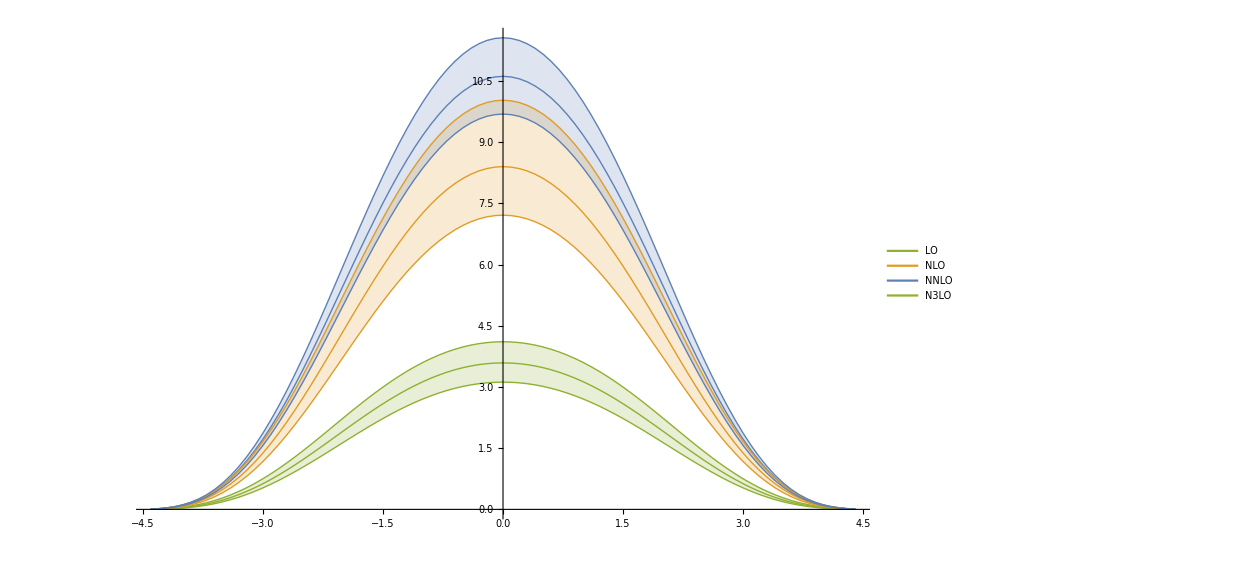

```mathematica
pp=ListLinePlot[dists
,PlotStyle->{{ColorData[97,"ColorList"][[3]],Thick},
{ColorData[97,"ColorList"][[2]],Thick},
{ColorData[97,"ColorList"][[1]],Thick},
{ColorData[97,"ColorList"][[3]],Thin},
{ColorData[97,"ColorList"][[3]],Thin},
{ColorData[97,"ColorList"][[2]],Thin},
{ColorData[97,"ColorList"][[2]],Thin},
{ColorData[97,"ColorList"][[1]],Thin},
{ColorData[97,"ColorList"][[1]],Thin},
{ColorData[97,"ColorList"][[4]],Thin},
{ColorData[97,"ColorList"][[4]],Thin}
},
Filling->{4->{1},5->{1},6->{2},7->{2},8->{3},9->{3},10->{4},11->{4}},
PlotLegends->Placed[LineLegend[{"LO\t     ","NLO\t","NNLO\t","N3LO\t"},LegendLayout->{"Row",3},LabelStyle->25],{0.85,0.8}]
]
```

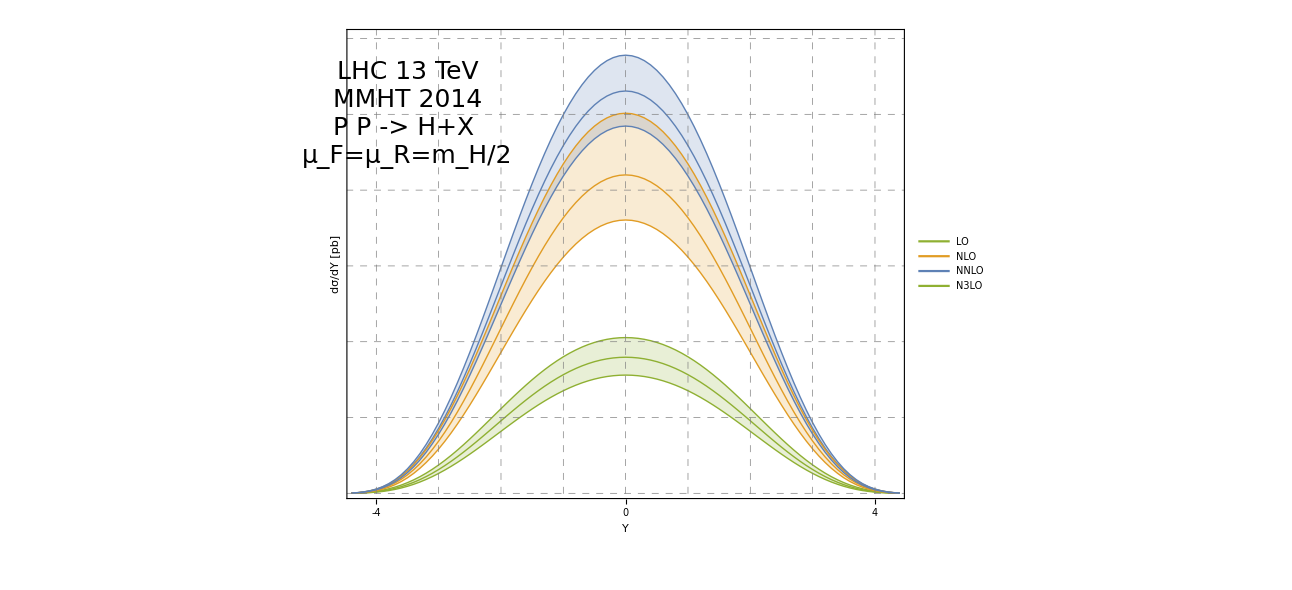

```mathematica
ppp=Show[pp,
PlotRange->{{-4.3,4.3},{0.1,12}},
Frame->True,
FrameTicks->{Table[{i,i} ,{i,-20,20}],2Table[{i,i},{i,-50,50}],None,None},
GridLines->{Table[i ,{i,-10,10}],Table[2i,{i,-10,12}]},
GridLinesStyle->Directive[Dashed,Thin,Gray],
AxesOrigin->{0,0},
FrameLabel->{" Y","dσ/dY [pb]"},
LabelStyle->Directive[Bold,30],
Epilog->Inset[Style["LHC 13 TeV\nMMHT 2014\nP P -> H+X \nμ_F=μ_R=m_H/2",25,TextAlignment->Left],{-3.5,10}]
]
```

## NNLO Rapidity Threshold expansion Only

```mathematica
NNLOCent=Get["Results/Rapidity_NNLO_mu62.5.m"];
NNLOMax=Get["Results/Rapidity_NNLO_mu125.m"];
NNLOMin=Get["Results/Rapidity_NNLO_mu31.25.m"];
```

```mathematica
Exp0=Get["Results/Rapidity_NNLOTHOnly_mu62.5_zb0.m"];
Exp1=Get["Results/Rapidity_NNLOTHOnly_mu62.5_zb1.m"];
Exp2=Get["Results/Rapidity_NNLOTHOnly_mu62.5_zb2.m"];
Exp3=Get["Results/Rapidity_NNLOTHOnly_mu62.5_zb3.m"];
Exp4=Get["Results/Rapidity_NNLOTHOnly_mu62.5_zb4.m"];
Exp5=Get["Results/Rapidity_NNLOTHOnly_mu62.5_zb5.m"];
Exp6=Get["Results/Rapidity_NNLOTHOnly_mu62.5_zb6.m"];
Exp7=Get["Results/Rapidity_NNLOTHOnly_mu62.5_zb7.m"];
```

```mathematica
xrange=NNLOCent[[;;,1]];
```

```mathematica
dists={NNLOCent,Exp1,Exp2,Exp3,Exp4,Exp5,Exp6,Exp7,NNLOMax,NNLOMin};
dists=Table[Table[{xrange[[j]],dists[[i,j,2]]/NNLOCent[[j,2]]},{j,1,Length[dists[[i]]]}],{i,1,Length[dists]}];
```

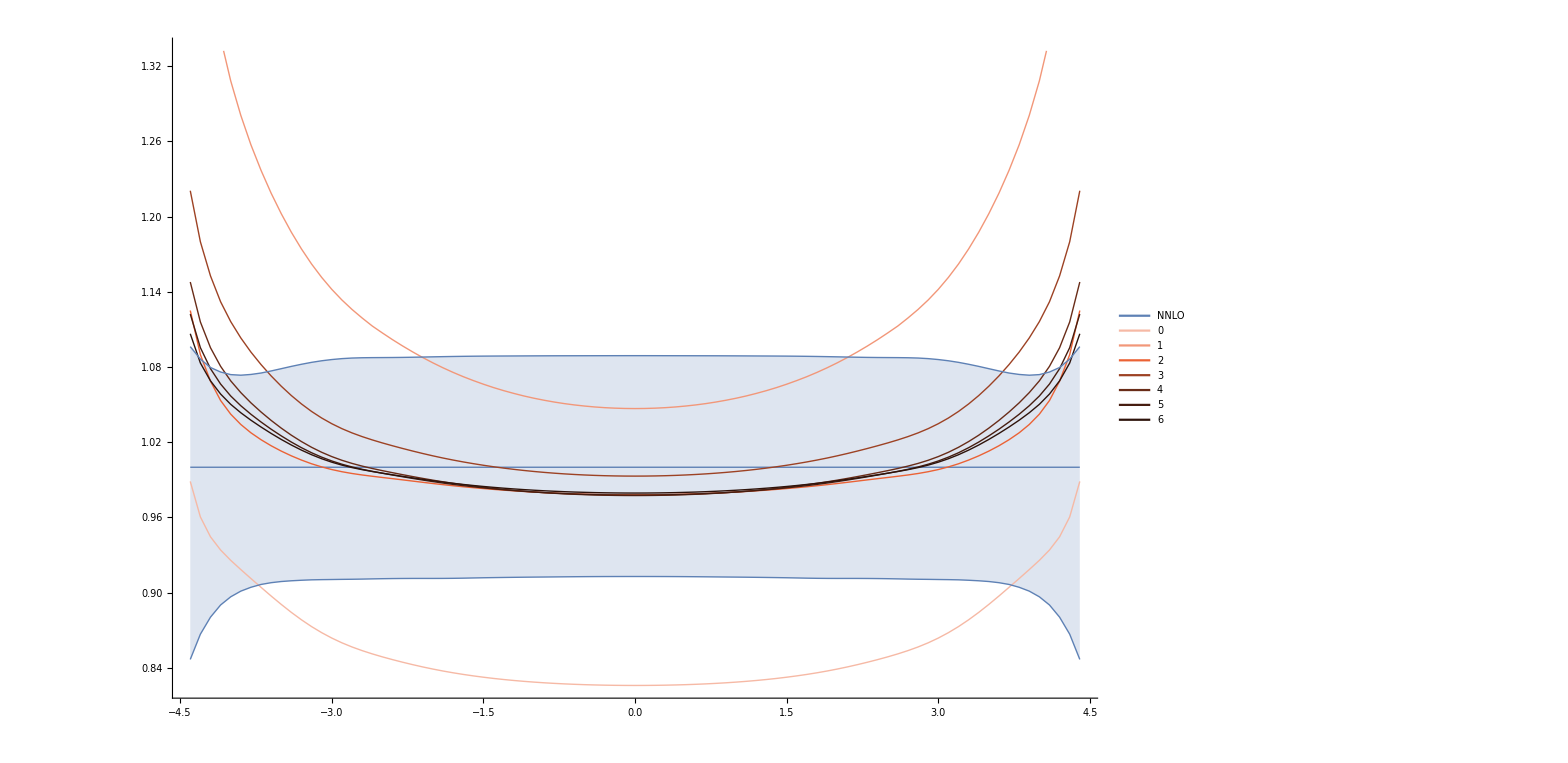

```mathematica
pp=ListLinePlot[dists
,PlotStyle->{{ColorData[97,"ColorList"][[1]],Thick},
{ColorData[97,"ColorList"][[4]]//Lighter//Lighter,Thick},
{ColorData[97,"ColorList"][[4]]//Lighter,Thick},
{ColorData[97,"ColorList"][[4]],Thick},
{ColorData[97,"ColorList"][[4]]//Darker,Thick},
{ColorData[97,"ColorList"][[4]]//Darker//Darker,Thick},
{ColorData[97,"ColorList"][[4]]//Darker//Darker//Darker,Thick},
{ColorData[97,"ColorList"][[4]]//Darker//Darker//Darker//Darker,Thick},
{ColorData[97,"ColorList"][[1]],Thin},
{ColorData[97,"ColorList"][[1]],Thin}
},
Filling->{9->{1},10->{1}},
PlotLegends->Placed[LineLegend[{"NNLO",0,1,2,3,4,5,6},LegendLayout->{"Row",2},LabelStyle->25],{0.5,0.8}],
InterpolationOrder->1
]
```

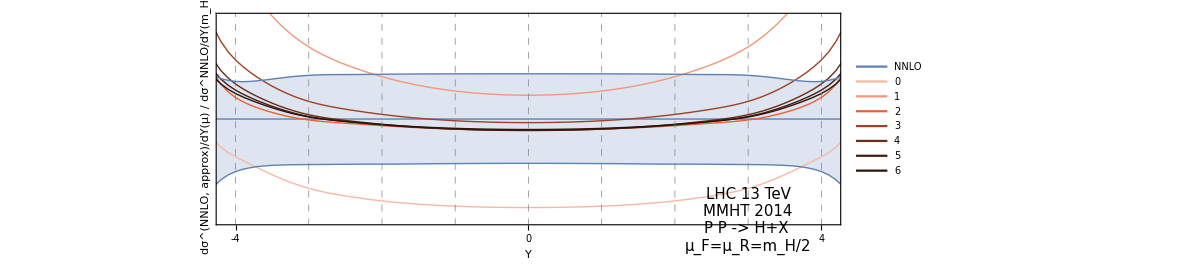

```mathematica
ppp=Show[pp,
PlotRange->{{-4.1,4.1},{0.8,1.2}},AspectRatio->0.3,
PlotRangePadding->.2,
Frame->True,
FrameTicks->{Table[{i,i} ,{i,-20,20}],0.1Table[{i,i},{i,-50,50}],None,None},
GridLines->{Table[i ,{i,-10,10}],Table[0.1i,{i,-10,200}]},
GridLinesStyle->Directive[Dashed,Thin,Gray],
AxesOrigin->{0,0},
FrameLabel->{" Y","dσ^(NNLO,  approx)/dY(μ) / dσ^NNLO/dY(m_H/2)"},
LabelStyle->Directive[Bold,15],
Epilog->Inset[Style["LHC 13 TeV\nMMHT 2014\nP P -> H+X \nμ_F=μ_R=m_H/2",15,TextAlignment->Left],{3,0.8}]
]
```

## NNLO Rapidity Threshold expansion Only μ=125

```mathematica
NNLOCent=Get["Results/Rapidity_NNLO_mu62.5.m"];
NNLOMax=Get["Results/Rapidity_NNLO_mu125.m"];
NNLOMin=Get["Results/Rapidity_NNLO_mu31.25.m"];
```

```mathematica
10Total[Exp5[[;;,2]]]/90
10Total[NNLOMax[[;;,2]]]/90
```

47.6471

44.1325

```mathematica
Exp0=Get["Results/Rapidity_NNLOTHOnly_mu125_zb0.m"];
Exp1=Get["Results/Rapidity_NNLOTHOnly_mu125_zb1.m"];
Exp2=Get["Results/Rapidity_NNLOTHOnly_mu125_zb2.m"];
Exp3=Get["Results/Rapidity_NNLOTHOnly_mu125_zb3.m"];
Exp4=Get["Results/Rapidity_NNLOTHOnly_mu125_zb4.m"];
Exp5=Get["Results/Rapidity_NNLOTHOnly_mu125_zb5.m"];
Exp6=Get["Results/Rapidity_NNLOTHOnly_mu125_zb6.m"];
Exp7=Get["Results/Rapidity_NNLOTHOnly_mu125_zb7.m"];
```

```mathematica
xrange=NNLOCent[[;;,1]];
```

```mathematica
dists={NNLOCent,NNLOMax,NNLOMin,Exp0,Exp1,Exp2,Exp3,Exp4,Exp5,Exp6,Exp7};
dists=Table[Table[{xrange[[j]],dists[[i,j,2]]/NNLOCent[[j,2]]},{j,1,Length[dists[[i]]]}],{i,1,Length[dists]}];
```

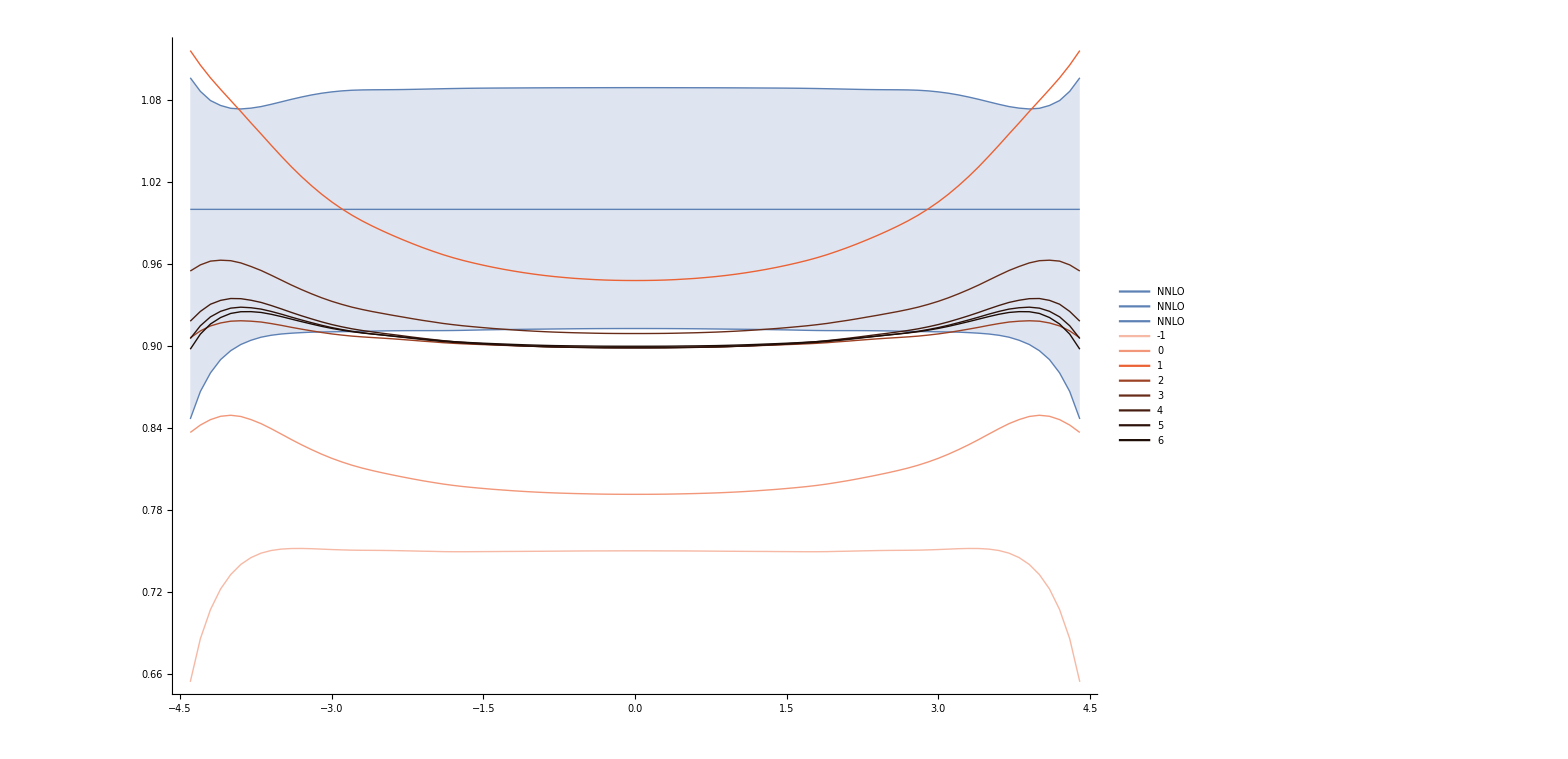

```mathematica
pp=ListLinePlot[dists
,PlotStyle->{{ColorData[97,"ColorList"][[1]],Thick},
{ColorData[97,"ColorList"][[1]],Thick},
{ColorData[97,"ColorList"][[1]],Thin},
{ColorData[97,"ColorList"][[4]]//Lighter//Lighter,Thick},
{ColorData[97,"ColorList"][[4]]//Lighter,Thick},
{ColorData[97,"ColorList"][[4]],Thick},
{ColorData[97,"ColorList"][[4]]//Darker,Thick},
{ColorData[97,"ColorList"][[4]]//Darker//Darker,Thick},
{ColorData[97,"ColorList"][[4]]//Darker//Darker//Darker,Thick},
{ColorData[97,"ColorList"][[4]]//Darker//Darker//Darker//Darker,Thick},
{ColorData[97,"ColorList"][[4]]//Darker//Darker//Darker//Darker//Darker,Thick}
},
Filling->{2->{1},3->{1}},
PlotLegends->Placed[LineLegend[{"NNLO\t","NNLO\t","NNLO",-1,0,1,2,3,4,5,6,7,8},LegendLayout->{"Row",4},LabelStyle->25],{0.85,0.2}],
PlotRange->All,InterpolationOrder->1
]
```

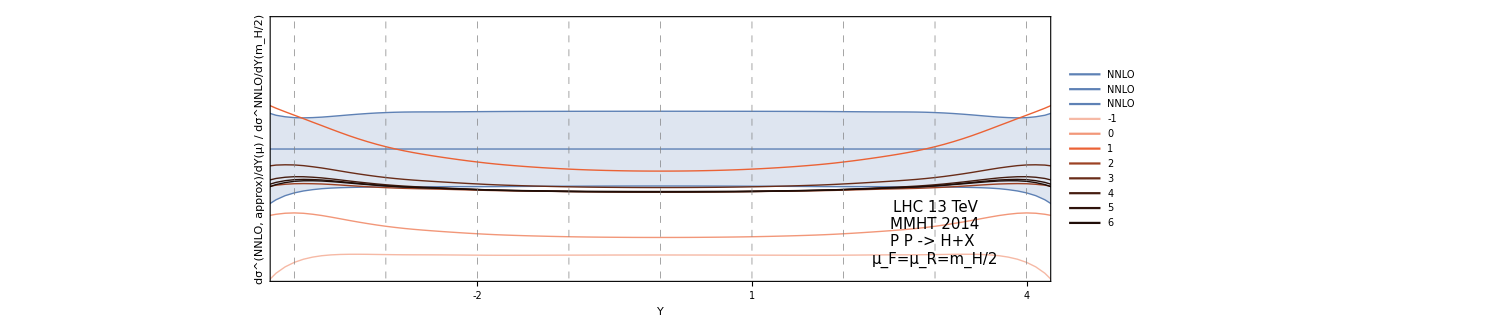

```mathematica
ppp=Show[pp,
PlotRange->{{-4.1,4.1},{0.7,1.3}},AspectRatio->0.3,
PlotRangePadding->.2,
Frame->True,
FrameTicks->{Table[{i,i} ,{i,-20,20}],0.1Table[{i,i},{i,-50,50}],None,None},
GridLines->{Table[i ,{i,-10,10}],Table[0.1i,{i,-10,200}]},
GridLinesStyle->Directive[Dashed,Thin,Gray],
AxesOrigin->{0,0},
FrameLabel->{" Y","dσ^(NNLO,  approx)/dY(μ) / dσ^NNLO/dY(m_H/2)"},
LabelStyle->Directive[Bold,15],
Epilog->Inset[Style["LHC 13 TeV\nMMHT 2014\nP P -> H+X \nμ_F=μ_R=m_H/2",15,TextAlignment->Left],{3,0.8}]
]
```

## NNLO Rapidity Approx -No Matching

```mathematica
NNLOCent=Get["Results/Rapidity_NNLO_mu62.5.m"];
NNLOMax=Get["Results/Rapidity_NNLO_mu125.m"];
NNLOMin=Get["Results/Rapidity_NNLO_mu31.25.m"];
```

```mathematica
Exp0=Get["Results/Rapidity_NNLO_mu62.5_Unmatched_zb0.m"];
Exp1=Get["Results/Rapidity_NNLO_mu62.5_Unmatched_zb1.m"];
Exp2=Get["Results/Rapidity_NNLO_mu62.5_Unmatched_zb2.m"];
Exp3=Get["Results/Rapidity_NNLO_mu62.5_Unmatched_zb3.m"];
Exp4=Get["Results/Rapidity_NNLO_mu62.5_Unmatched_zb4.m"];
Exp5=Get["Results/Rapidity_NNLO_mu62.5_Unmatched_zb5.m"];
Exp6=Get["Results/Rapidity_NNLO_mu62.5_Unmatched_zb6.m"];
Exp7=Get["Results/Rapidity_NNLO_mu62.5_Unmatched_zb7.m"];
```

```mathematica
dists={NNLOCent,Exp1,Exp2,Exp3,Exp4,Exp5,Exp6,Exp7,NNLOMax,NNLOMin};
dists=Table[Table[{xrange[[j]],dists[[i,j,2]]/NNLOCent[[j,2]]},{j,1,Length[dists[[i]]]}],{i,1,Length[dists]}];
```

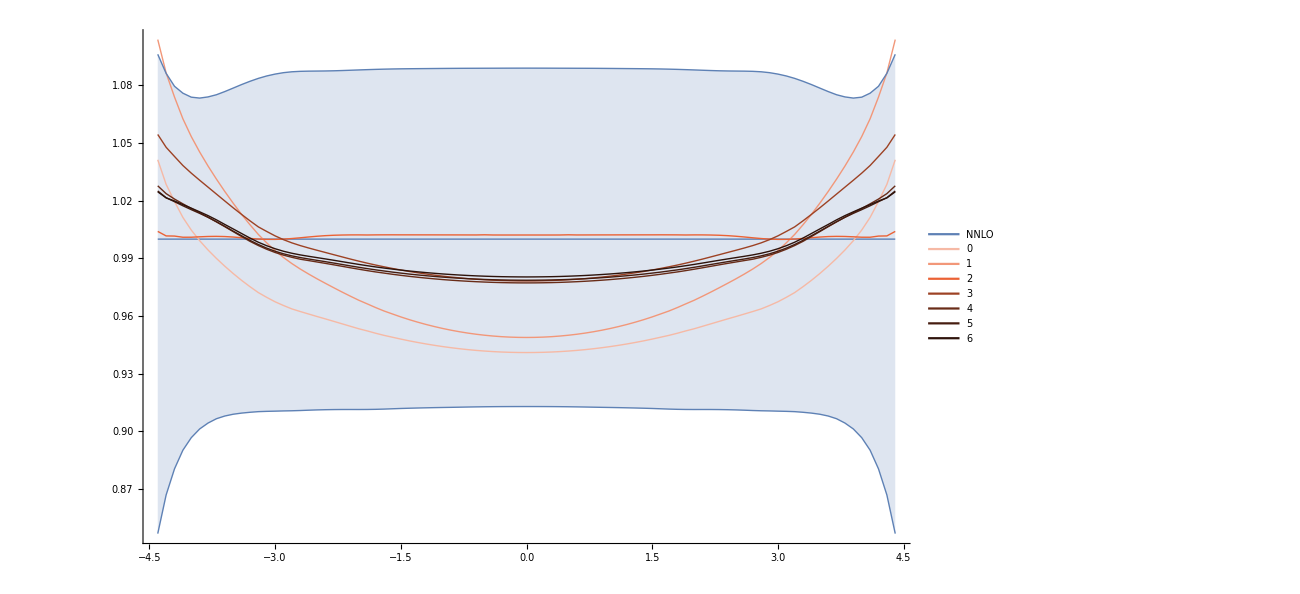

```mathematica
pp=ListLinePlot[dists
,PlotStyle->{{ColorData[97,"ColorList"][[1]],Thick},
{ColorData[97,"ColorList"][[4]]//Lighter//Lighter,Thick},
{ColorData[97,"ColorList"][[4]]//Lighter,Thick},
{ColorData[97,"ColorList"][[4]],Thick},
{ColorData[97,"ColorList"][[4]]//Darker,Thick},
{ColorData[97,"ColorList"][[4]]//Darker//Darker,Thick},
{ColorData[97,"ColorList"][[4]]//Darker//Darker//Darker,Thick},
{ColorData[97,"ColorList"][[4]]//Darker//Darker//Darker//Darker,Thick},
{ColorData[97,"ColorList"][[1]],Thin},
{ColorData[97,"ColorList"][[1]],Thin}
},
Filling->{9->{1},10->{1}},
PlotLegends->Placed[LineLegend[{"NNLO",0,1,2,3,4,5,6},LegendLayout->{"Row",2},LabelStyle->25],{0.5,0.8}],
InterpolationOrder->1
]
```

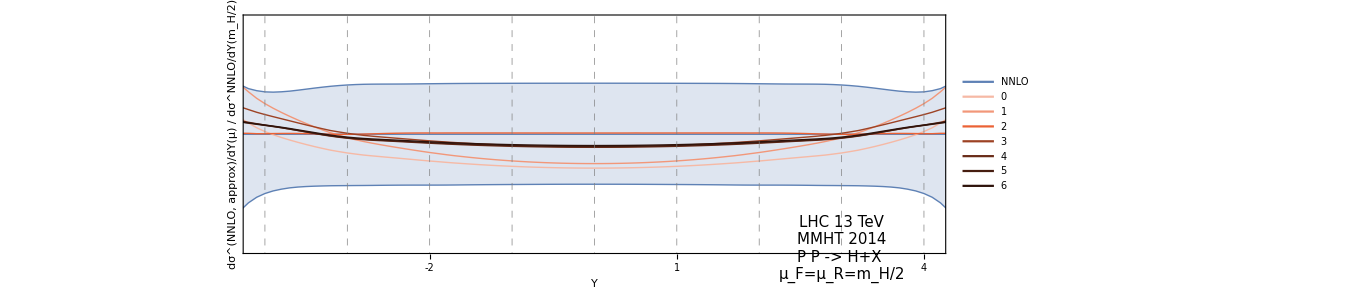

```mathematica
ppp=Show[pp,
PlotRange->{{-4.1,4.1},{0.8,1.2}},
AspectRatio->0.3,
Frame->True,
FrameTicks->{Table[{i,i} ,{i,-20,20}],0.1Table[{i,i},{i,-50,50}],None,None},
GridLines->{Table[i ,{i,-10,10}],Table[0.1i,{i,-10,200}]},
GridLinesStyle->Directive[Dashed,Thin,Gray],
AxesOrigin->{0,0},
FrameLabel->{" Y","dσ^(NNLO,  approx)/dY(μ) / dσ^NNLO/dY(m_H/2)"},
LabelStyle->Directive[Bold,15],
Epilog->Inset[Style["LHC 13 TeV\nMMHT 2014\nP P -> H+X \nμ_F=μ_R=m_H/2",15,TextAlignment->Left],{3,0.8}],
ImageSize->1000
]
```

## NNLO Rapidity Threshold expansion+ Matching

```mathematica
NNLOCent=Get["Results/Rapidity_NNLO_mu62.5.m"];
NNLOMax=Get["Results/Rapidity_NNLO_mu125.m"];
NNLOMin=Get["Results/Rapidity_NNLO_mu31.25.m"];
```

```mathematica
Exp1=Get["Results/Rapidity_NNLO_mu62.5_THOnlyMatched_zb1.m"];
Exp2=Get["Results/Rapidity_NNLO_mu62.5_THOnlyMatched_zb2.m"];
Exp3=Get["Results/Rapidity_NNLO_mu62.5_THOnlyMatched_zb3.m"];
Exp4=Get["Results/Rapidity_NNLO_mu62.5_THOnlyMatched_zb4.m"];
Exp5=Get["Results/Rapidity_NNLO_mu62.5_THOnlyMatched_zb5.m"];
Exp6=Get["Results/Rapidity_NNLO_mu62.5_THOnlyMatched_zb6.m"];
Exp7=Get["Results/Rapidity_NNLO_mu62.5_THOnlyMatched_zb7.m"];
```

```mathematica
xrange=NNLOCent[[;;,1]];
```

```mathematica
dists={NNLOCent,Exp1,Exp2,Exp3,Exp4,Exp5,Exp6,Exp7,NNLOMax,NNLOMin};
dists=Table[Table[{xrange[[j]],dists[[i,j,2]]/NNLOCent[[j,2]]},{j,1,Length[dists[[i]]]}],{i,1,Length[dists]}];
```

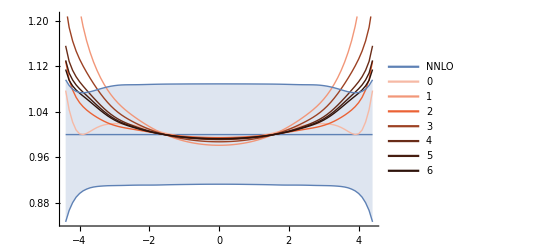

```mathematica
pp=ListLinePlot[dists
,PlotStyle->{{ColorData[97,"ColorList"][[1]],Thick},
{ColorData[97,"ColorList"][[4]]//Lighter//Lighter,Thick},
{ColorData[97,"ColorList"][[4]]//Lighter,Thick},
{ColorData[97,"ColorList"][[4]],Thick},
{ColorData[97,"ColorList"][[4]]//Darker,Thick},
{ColorData[97,"ColorList"][[4]]//Darker//Darker,Thick},
{ColorData[97,"ColorList"][[4]]//Darker//Darker//Darker,Thick},
{ColorData[97,"ColorList"][[4]]//Darker//Darker//Darker//Darker,Thick},
{ColorData[97,"ColorList"][[1]],Thin},
{ColorData[97,"ColorList"][[1]],Thin}
},
Filling->{9->{1},10->{1}},
PlotLegends->Placed[LineLegend[{"NNLO",0,1,2,3,4,5,6},LegendLayout->{"Row",2},LabelStyle->25],{0.5,0.8}],
InterpolationOrder->1
]
```

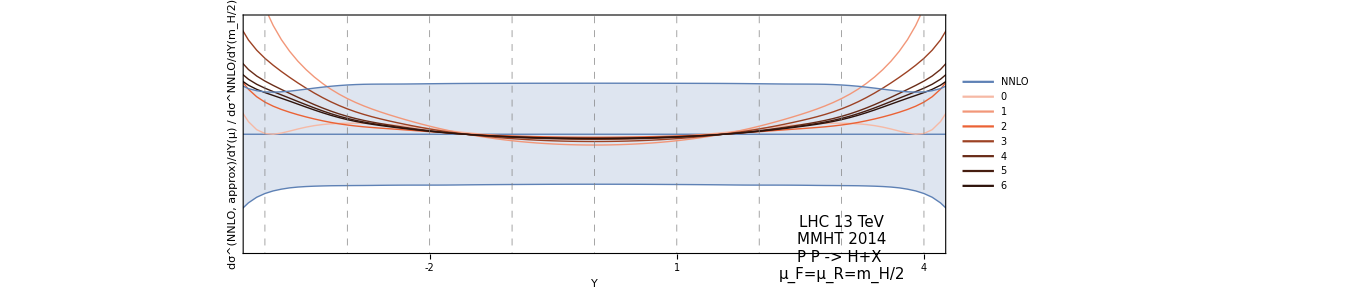

```mathematica
ppp=Show[pp,
PlotRange->{{-4.1,4.1},{0.8,1.2}},
AspectRatio->0.3,
Frame->True,
FrameTicks->{Table[{i,i} ,{i,-20,20}],0.1Table[{i,i},{i,-50,50}],None,None},
GridLines->{Table[i ,{i,-10,10}],Table[0.1i,{i,-10,200}]},
GridLinesStyle->Directive[Dashed,Thin,Gray],
AxesOrigin->{0,0},
FrameLabel->{" Y","dσ^(NNLO,  approx)/dY(μ) / dσ^NNLO/dY(m_H/2)"},
LabelStyle->Directive[Bold,15],
Epilog->Inset[Style["LHC 13 TeV\nMMHT 2014\nP P -> H+X \nμ_F=μ_R=m_H/2",15,TextAlignment->Left],{3,0.8}],
ImageSize->1000
]
```

## NNLO Rapidity Approx

```mathematica
NNLOCent=Get["Results/Rapidity_NNLO_mu62.5.m"];
NNLOMax=Get["Results/Rapidity_NNLO_mu125.m"];
NNLOMin=Get["Results/Rapidity_NNLO_mu31.25.m"];
```

```mathematica
xrange=NNLOCent[[;;,1]];
```

```mathematica
Exp0=Get["Results/Rapidity_NNLO_mu62.5_zb0.m"];
Exp1=Get["Results/Rapidity_NNLO_mu62.5_zb1.m"];
Exp2=Get["Results/Rapidity_NNLO_mu62.5_zb2.m"];
Exp3=Get["Results/Rapidity_NNLO_mu62.5_zb3.m"];
Exp4=Get["Results/Rapidity_NNLO_mu62.5_zb4.m"];
Exp5=Get["Results/Rapidity_NNLO_mu62.5_zb5.m"];
Exp6=Get["Results/Rapidity_NNLO_mu62.5_zb6.m"];
Exp7=Get["Results/Rapidity_NNLO_mu62.5_zb7.m"];
```

```mathematica
dists={NNLOCent,Exp1,Exp2,Exp3,Exp4,Exp5,Exp6,Exp7,NNLOMax,NNLOMin};
dists=Table[Table[{xrange[[j]],dists[[i,j,2]]/NNLOCent[[j,2]]},{j,1,Length[dists[[i]]]}],{i,1,Length[dists]}];
```

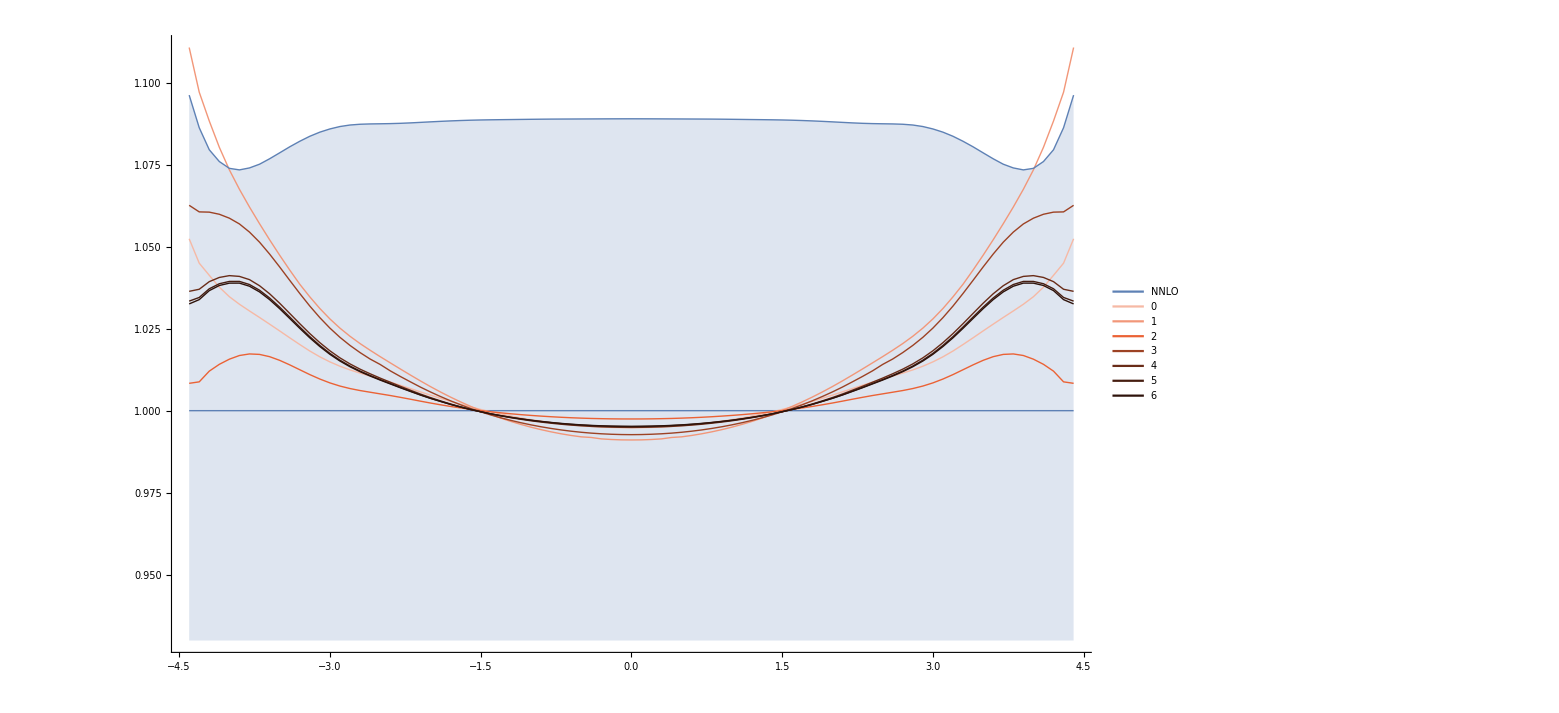

```mathematica
pp=ListLinePlot[dists
,PlotStyle->{{ColorData[97,"ColorList"][[1]],Thick},
{ColorData[97,"ColorList"][[4]]//Lighter//Lighter,Thick},
{ColorData[97,"ColorList"][[4]]//Lighter,Thick},
{ColorData[97,"ColorList"][[4]],Thick},
{ColorData[97,"ColorList"][[4]]//Darker,Thick},
{ColorData[97,"ColorList"][[4]]//Darker//Darker,Thick},
{ColorData[97,"ColorList"][[4]]//Darker//Darker//Darker,Thick},
{ColorData[97,"ColorList"][[4]]//Darker//Darker//Darker//Darker,Thick},
{ColorData[97,"ColorList"][[1]],Thin},
{ColorData[97,"ColorList"][[1]],Thin}
},
Filling->{9->{1},10->{1}},
PlotLegends->Placed[LineLegend[{"NNLO",0,1,2,3,4,5,6},LegendLayout->{"Row",2},LabelStyle->25],{0.5,0.8}],
InterpolationOrder->1
]
```

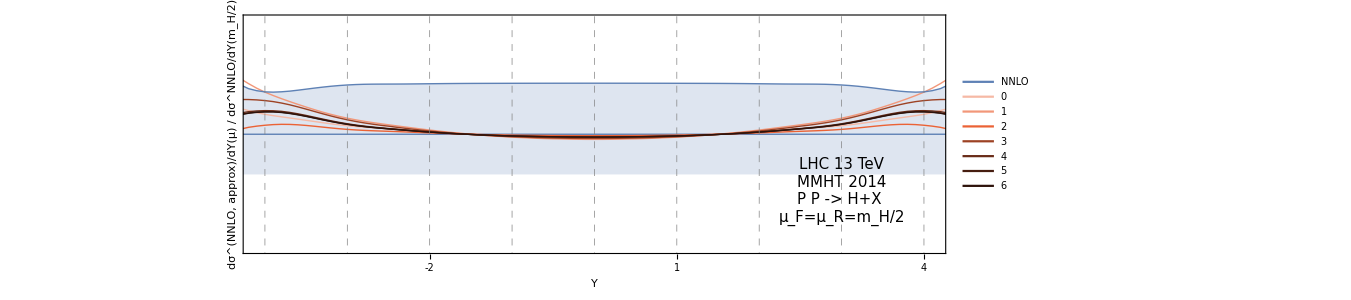

```mathematica
ppp=Show[pp,
PlotRange->{{-4.1,4.1},{0.8,1.2}},
AspectRatio->0.3,
Frame->True,
FrameTicks->{Table[{i,i} ,{i,-20,20}],0.1Table[{i,i},{i,-50,50}],None,None},
GridLines->{Table[i ,{i,-10,10}],Table[0.1i,{i,-10,200}]},
GridLinesStyle->Directive[Dashed,Thin,Gray],
AxesOrigin->{0,0},
FrameLabel->{" Y","dσ^(NNLO,  approx)/dY(μ) / dσ^NNLO/dY(m_H/2)"},
LabelStyle->Directive[Bold,15],
Epilog->Inset[Style["LHC 13 TeV\nMMHT 2014\nP P -> H+X \nμ_F=μ_R=m_H/2",15,TextAlignment->Left],{3,0.9}],
ImageSize->1000
]
```